```mathematica
Subscript[z, 1][ s_,λ_]= ((λ + 1)Exp[-s] + Sqrt[(1+ λ)^2 Exp[-2s] - 4 λ ])/2;
Subscript[z, 2][ s_,λ_]= ((λ + 1)Exp[-s] - Sqrt[(1+ λ)^2 Exp[-2s] - 4 λ ])/2;
γ[s_,λ_] = Exp[s](Subscript[z, 1][ s,λ]-Subscript[z, 2][ s,λ]);
tF[s_,λ_,t_] =η( ((1-Subscript[z, 2][ s,λ])Subscript[z, 1][ s,λ]- (1-Subscript[z, 1][ s,λ])Subscript[z, 2][ s,λ] Exp[γ[ s,λ] t])/((1-Subscript[z, 2][ s,λ])- (1-Subscript[z, 1][ s,λ])Exp[γ[ s,λ] t])-1) //FullSimplify
```

(2 (-1+ⅇ^s) η (1+λ))/(1+λ+ⅇ^s (-2+√(-4 λ+ⅇ^(-2 s) (1+λ)^2)+(2 √(-4 λ+ⅇ^(-2 s) (1+λ)^2))/(-1+ⅇ^(ⅇ^s t √(-4 λ+ⅇ^(-2 s) (1+λ)^2)))))

```mathematica
SubStar[s][λ_] =1/2 Log[(λ + 1)^2/(4λ)]
```

1/2 Log[(1+λ)^2/(4 λ)]

```mathematica
F[s_,λ_]=Subscript[z, 2][s,λ]
```

1/2 (ⅇ^-s (1+λ)-√(-4 λ+ⅇ^(-2 s) (1+λ)^2))

```mathematica
expZ[λ_,ϕ_]=Collect[Normal@Series[Simplify[F[s,λ]/.s->SubStar[s][λ]+χ ϕ^2]/.χ->-1,{ϕ,0,3}],ϕ,FullSimplify]
```

(1+λ)/(√(2+1/λ+λ))-√2 √λ ϕ+((1+λ) ϕ^2)/(√(2+1/λ+λ))-(√λ ϕ^3)/(√2)

```mathematica
$Assumptions=ϕ>0
```

ϕ>0

```mathematica
Subscript[expZ, c][ϵ_,ϕ_]=Collect[Series[Normal@Series[Simplify[expZ[λ,ϕ]/.λ->1+ϵ],{ϵ,0,3}],{ϵ,0,1}]/.χ->-1,ϕ,Simplify]
```

(2+ϵ)/2-((2+ϵ) ϕ)/(√2)+1/2 (2+ϵ) ϕ^2-((2+ϵ) ϕ^3)/(2 √2)

```mathematica
Solve[%==0,ϕ]
```

$Aborted

Time Dependent Case

```mathematica
$Assumptions=λ>0
```

λ>0

```mathematica
exptZ[λ_,ϕ_,t_]=Collect[Normal@Series[tF[s,λ,t]/.s->SubStar[s][λ]+χ ϕ,{ϕ,0,4}],ϕ]//FullSimplify
```

(t η (1+λ) (3 t^11 (1+λ)^10 (-1+λ^3 (-5+√(2+1/λ+λ))+5 λ^2 (-3+2 √(2+1/λ+λ))+λ (-11+5 √(2+1/λ+λ))) ϕ^4 χ^4+72 t^10 λ (1+λ)^9 (-4+√(2+1/λ+λ)+λ^2 (-4+√(2+1/λ+λ))+λ (-8+6 √(2+1/λ+λ))) ϕ^4 χ^4+12 t^9 (1+λ)^8 ϕ^3 χ^3 (-5 (1+2 ϕ χ)+λ (-55+25 √(2+1/λ+λ)+(-176+50 √(2+1/λ+λ)) ϕ χ)+λ^3 (-25+5 √(2+1/λ+λ)+(-248+76 √(2+1/λ+λ)) ϕ χ)+λ^2 (-75+50 √(2+1/λ+λ)+(-414+298 √(2+1/λ+λ)) ϕ χ))+40 t^8 λ (1+λ)^7 ϕ^3 χ^3 (-120+30 √(2+1/λ+λ)+(-195+45 √(2+1/λ+λ)) ϕ χ+λ^2 (-120+30 √(2+1/λ+λ)+7 (-67+26 √(2+1/λ+λ)) ϕ χ)+λ (-240+180 √(2+1/λ+λ)+(-664+437 √(2+1/λ+λ)) ϕ χ))+6300 t^2 λ (1+λ) (432 (-4+√(2+1/λ+λ))+216 (-1+√(2+1/λ+λ)) ϕ χ-36 (1+√(2+1/λ+λ)) ϕ^2 χ^2-36 (-1+√(2+1/λ+λ)) ϕ^3 χ^3+33 (1+√(2+1/λ+λ)) ϕ^4 χ^4+λ^2 (432 (-4+√(2+1/λ+λ))+(-744+480 √(2+1/λ+λ)) ϕ χ+12 (-17+26 √(2+1/λ+λ)) ϕ^2 χ^2+44 (1+4 √(2+1/λ+λ)) ϕ^3 χ^3+(67+98 √(2+1/λ+λ)) ϕ^4 χ^4)+λ (-3456+2592 √(2+1/λ+λ)+(-960+264 √(2+1/λ+λ)) ϕ χ+60 (-4+√(2+1/λ+λ)) ϕ^2 χ^2+(80+68 √(2+1/λ+λ)) ϕ^3 χ^3+(100+113 √(2+1/λ+λ)) ϕ^4 χ^4))+30 t^7 (1+λ)^6 ϕ^2 χ^2 (-7 (6+ϕ χ (6+5 ϕ χ))+λ (-462+210 √(2+1/λ+λ)+ϕ χ (-822+210 √(2+1/λ+λ)+(-745+175 √(2+1/λ+λ)) ϕ χ))+λ^3 (-210+42 √(2+1/λ+λ)+ϕ χ (-1290+402 √(2+1/λ+λ)+(-2527+1307 √(2+1/λ+λ)) ϕ χ))+λ^2 (-630+420 √(2+1/λ+λ)+ϕ χ (-2070+1500 √(2+1/λ+λ)+(-3237+1790 √(2+1/λ+λ)) ϕ χ)))+60 t^6 λ (1+λ)^5 ϕ^2 χ^2 (336 (-4+√(2+1/λ+λ))+7 ϕ χ (-138+30 √(2+1/λ+λ)+(-115+31 √(2+1/λ+λ)) ϕ χ)+λ (-2688+2016 √(2+1/λ+λ)+ϕ χ (-3936+2514 √(2+1/λ+λ)+(-4052+1803 √(2+1/λ+λ)) ϕ χ))+λ^2 (336 (-4+√(2+1/λ+λ))+ϕ χ (-2970+1212 √(2+1/λ+λ)+(-3247+2440 √(2+1/λ+λ)) ϕ χ)))+75600 λ^2 (-48+24 √(2+1/λ+λ)+√(2+1/λ+λ) ϕ χ (24+ϕ χ (12+ϕ χ (4+ϕ χ))))+420 t^5 (1+λ)^4 ϕ χ (-15 (6+ϕ^2 χ^2)+λ (-990+450 √(2+1/λ+λ)-ϕ χ (336+ϕ χ (249-75 √(2+1/λ+λ)+190 ϕ χ)))+λ^2 (-1350+900 √(2+1/λ+λ)+ϕ χ (-1344+1008 √(2+1/λ+λ)+ϕ χ (-1377+654 √(2+1/λ+λ)+124 (-7+3 √(2+1/λ+λ)) ϕ χ)))+λ^3 (-450+90 √(2+1/λ+λ)+ϕ χ (336 (-3+√(2+1/λ+λ))+ϕ χ (-1143+663 √(2+1/λ+λ)+226 (-3+4 √(2+1/λ+λ)) ϕ χ))))+37800 t (2 λ^2 (-192+144 √(2+1/λ+λ)+24 (-3+√(2+1/λ+λ)) ϕ χ+12 (-1+√(2+1/λ+λ)) ϕ^2 χ^2+4 (3+√(2+1/λ+λ)) ϕ^3 χ^3+(11+√(2+1/λ+λ)) ϕ^4 χ^4)+λ^3 (-288+96 √(2+1/λ+λ)+(-72+96 √(2+1/λ+λ)) ϕ χ+12 (-1+4 √(2+1/λ+λ)) ϕ^2 χ^2+4 (3+4 √(2+1/λ+λ)) ϕ^3 χ^3+(11+4 √(2+1/λ+λ)) ϕ^4 χ^4)+λ (-96+ϕ χ (-72+ϕ χ (-12+ϕ χ (12+11 ϕ χ)))))+3150 t^3 (1+λ)^2 (3 (-4+ϕ χ) (24+12 ϕ χ+ϕ^3 χ^3)+λ^2 (-4320+2880 √(2+1/λ+λ)+360 (-3+2 √(2+1/λ+λ)) ϕ χ+12 (-59+20 √(2+1/λ+λ)) ϕ^2 χ^2+12 (-23+10 √(2+1/λ+λ)) ϕ^3 χ^3+7 (19+20 √(2+1/λ+λ)) ϕ^4 χ^4)+λ^3 (288 (-5+√(2+1/λ+λ))+216 (-5+2 √(2+1/λ+λ)) ϕ χ+12 (-49+36 √(2+1/λ+λ)) ϕ^2 χ^2+12 (-13+30 √(2+1/λ+λ)) ϕ^3 χ^3+(83+252 √(2+1/λ+λ)) ϕ^4 χ^4)+λ (-3168+1440 √(2+1/λ+λ)+ϕ χ (-72+ϕ χ (-84+ϕ χ (-132+53 ϕ χ)))))+315 t^4 (1+λ)^3 (λ^2 (-9360+5400 √(2+1/λ+λ)+360 (-17+14 √(2+1/λ+λ)) ϕ χ+12 (-417+226 √(2+1/λ+λ)) ϕ^2 χ^2+12 (-229+68 √(2+1/λ+λ)) ϕ^3 χ^3+(-561+838 √(2+1/λ+λ)) ϕ^4 χ^4)+λ^3 (360 (-6+√(2+1/λ+λ))+360 (-11+3 √(2+1/λ+λ)) ϕ χ+12 (-327+151 √(2+1/λ+λ)) ϕ^2 χ^2+36 (-63+61 √(2+1/λ+λ)) ϕ^3 χ^3+(-411+2143 √(2+1/λ+λ)) ϕ^4 χ^4)+15 (-144+24 √(2+1/λ+λ)+ϕ χ (24-ϕ χ (12+ϕ χ (-4+ϕ χ))))+λ (-9360+5400 √(2+1/λ+λ)-5 ϕ χ (360+72 √(2+1/λ+λ)+ϕ χ (252-132 √(2+1/λ+λ)+ϕ χ (84-12 √(2+1/λ+λ)+(33+√(2+1/λ+λ)) ϕ χ)))))))/(113400 λ^2 (2+t (1+λ-√(2+1/λ+λ)))^5)

```mathematica
$Assumptions=ϕ>0
```

ϕ>0

```mathematica
Subscript[exptZ, c][ϵ_,ϕ_]=Collect[Series[Normal@Series[exptZ[λ,ϕ,t]/.λ->1+ϵ,{ϵ,0,3}],{ϵ,0,1}],ϕ]//FullSimplify
```

1/2520 t η ϕ χ (-2520 (-2+(-1+t) ϵ)-420 (-3 (2+ϵ)+t (-3 (4+ϵ)+8 t (-1+t ϵ))) ϕ χ-28 (-12 t (15+2 t (15+2 t (5+2 t)))+t (-75+2 t (-90+t (45+60 t+68 t^2))) ϵ-15 (2+ϵ)) ϕ^2 χ^2+(4 t (735+2 t (1505+2 t (1155+2 t (525+34 t (7+2 t)))))+t (1365+4 t (1890+t (1715-4 t (-105+t (665+8 t (56+31 t)))))) ϵ+105 (2+ϵ)) ϕ^3 χ^3)

```mathematica
Series[Subscript[exptZ, c][ϵ,ϕ],{ϕ,0,3}]
```

t (2-(-1+t) ϵ) η χ ϕ-1/6 (t (-3 (2+ϵ)+t (-3 (4+ϵ)+8 t (-1+t ϵ))) η χ^2) ϕ^2-1/90 (t (-12 t (15+2 t (15+2 t (5+2 t)))+t (-75+2 t (-90+t (45+60 t+68 t^2))) ϵ-15 (2+ϵ)) η χ^3) ϕ^3+O[ϕ]^4

```mathematica
S1=SeriesCoefficient[%,1]//FullSimplify
```

t (2+ϵ-t ϵ) η χ

```mathematica
S2=SeriesCoefficient[%%,2]//FullSimplify
```

1/6 t (8 t^2-8 t^3 ϵ+3 (2+ϵ)+3 t (4+ϵ)) η χ^2

```mathematica
S3=SeriesCoefficient[%%%,3]//FullSimplify
```

1/90 t (30+12 t (15+2 t (15+2 t (5+2 t)))+15 ϵ+t (75-2 t (-90+t (45+60 t+68 t^2))) ϵ) η χ^3

```mathematica
s1[t_]=S1
```

t (2+ϵ-t ϵ) η χ

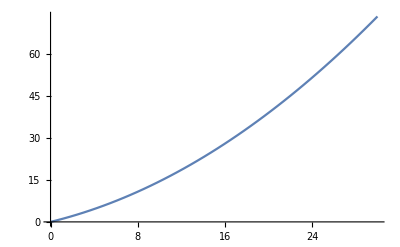

```mathematica
Plot[s1[t]/.{χ->1,η->1/2,ϵ->-10^-1},{t,0,30},PlotRange->Full]
```

```mathematica
s2[t_]=S2
```

1/12 t (8 t^2-8 t^3 ϵ+3 (2+ϵ)+3 t (4+ϵ)) χ^2

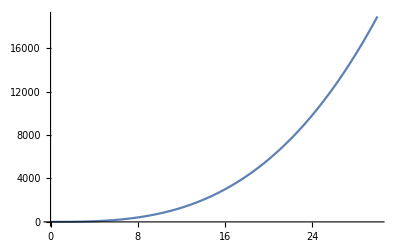

```mathematica
Plot[s2[t]/.{χ->1,η->1/2,ϵ->0},{t,0,30},PlotRange->Full]
```

```mathematica
s3[t_]=S3
```

1/180 t (30+12 t (15+2 t (15+2 t (5+2 t)))+15 ϵ+t (75-2 t (-90+t (45+60 t+68 t^2))) ϵ) χ^3

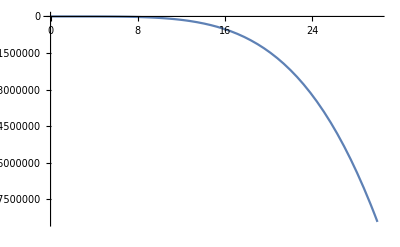

```mathematica
Plot[s3[t]/.{χ->-1,η->1/2,ϵ->10^-2},{t,0,30},PlotRange->Full]
```